# STRANGE QUARK MASS FROM QCD SUM RULES

```mathematica
(*Written in Mathematica 11.3*)
```

This notebook provides code to calculate the mass of the strange quark using finite energy sum rules. It is intended as a supplement to the dissertation: Mes ‘Light Quark Masses from QCD Sum Rules’, (2019). 

Always check for the latest version in the git repository: 
https://github.com/AlexesMes/light-quark-masses . 
(This repository also contains additional resources which would be of interest to the reader.) 

Please cite the journal paper if any part of this code is used in your own research.
This work is licensed under the Creative Commons Attribution-ShareAlike 4.0 International License. To view a copy of this license, visit http://creativecommons.org/licenses/by-sa/4.0/ or send a letter to Creative Commons, PO Box 1866, Mountain View, CA 94042, USA.

Mathematica code written by A. Mes
ORCID ID: 0000-0002-1187-7655
Corresponding email address: MSXALE002@myuct.ac.za
Last revised: 28-12-2018.

```mathematica
<<GeneralUtilities` 
<<ErrorBarPlots`
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False]; (*This supresses undeflow warning messages*)
```

### Initialize Constants - Global Inputs

```mathematica
(*Threshold energy. Source: Dominguez, Nasrallah, Rontsch, Schilcher 'Strange quark mass from Finite Energy QCD sum rules to five loops'(2008).*)
sth=(mpi+mk)^2;
(*Pion Pole data (mπ and fπ)[in MeV]. Source: (Particle Data Group), Phys.Rev.D 98,030001 (2018),'Leptonic decays of charged pseudoscalar mesons'.*)
mpi =134.9770/1000;fpi = 92.07/1000;  
(*Kaon Pole data (Subscript[m, K] and Subscript[f, K]) [in MeV]. Source: (Particle Data Group), Phys.Rev.D 98,030001 (2018),'Leptonic decays of charged pseudoscalar mesons'.*)
mk = 493.677/1000;fk = 110.03/1000;
(*sint0 = (mτ)^2 = initial reference energy, aint0 = (coupling strength at s = sint0)/ π. uncert0 = (uncertainty in coupling strength at s = sint0)/ π. 
Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
sint0= (1.77686)^2; aint0=0.3205/Pi;uncert0 = 0.0183/Pi;
(*Three light quark flavours: up, down and strange*)
nf=3; 
(*The up- and down- quark mass, where Subscript[m, ud]=(Subscript[m, u]+Subscript[m, d])/2. The world-average of Subscript[m, ud] is used (as given in the PDG): Subscript[m, ud](2 GeV) = 3.5 + 0.5 - 0.2 MeV. Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
mud=3.5/1000;
(*The strange quark mass used to evaluate supression terms in the correlator (non-perturbative effects) for this numerical illustration. The world-average of Subscript[m, s] is used (as given in the PDG): Subscript[m, s](2 GeV) = 95 + 9 - 3 MeV. Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
ms=95/1000;
(*Gluon condensate, <α/π G^2>.
 Source: Dominguez, Hernandez, Schilcher, 'Determination of the gluon condensate from data in the charm-quark region' (2015).*)
GluonCon= 0.037; uncertGluonCon=0.015; 
(*Light quark condensate, <qq>: calculated using found the GMOR (Gell-Mann Oakes Renner Relation) relation. Source: K.G. Chetyrkin,  A. Khodjamirian, 'Strange quark mass from pseudoscalar sum rule with accuracy', Eur. Phys. J. C 46,721-728 (2006). Corrections to GMOR relation = 6.5%. Source: Bordess, Moodley, 'Chiral Corrections to SU2 X SU2 GMOR relation',(2010).*)
LQuarkCon = (-(fpi^2*mpi^2*(1-0.062)))/(2*mud) ;
(*The ratio of strange to non-strange quark condensates: <ss>/<qq> = 0.8 ± 0.1. Source: Ioffe,'QCD at Low Energies',arXiv:hep-ph/0502148v2 (2005).*)
SQuarkCon = 0.8*LQuarkCon;
(*Ratio ms/mud=27.3 (where mud = (mu +md)/2), used to seperate the strange quark mass from the up- and down-quark mass (since the FESR determines (ms+ mud)). Note: this average is entirely dominated by LQCD determinations. Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
ratioms=(1/(1+1/27.3));
```

Note: The Particle Data Group gives the world average of the strong coupling to be: α_s(m_Z^2)=0.1181+ 0.0011 . (Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018)).
We have then used version 3 of RunDec (a Mathematica package for running and decoupling of the strong coupling and quark masses)  to run the coupling to the m_τ scale, decoupling over flavour thresholds. We find α_s(m_τ^2)=0.3205 + 0.0183 . (Source: K. Chetyrkin, J. Kühn and M. Steinhauser, arXiv preprint hep-ph/0004189 (2000)).

# Hadronic Spectrum

In the hadronic sector, the spectral function of the current correlator ψ_5(q^2), involves the kaon pole followed by the kaonic resonance contribution. This section elaborates on the method to model the hadronic resonances using a sum of Breit-Wigner forms.

### Choosing a Kernel

There is a freedom in the choice of kernel P_5(s). The most effective kernel is: P_5(s) = (s-a)(s-s_0). This is the integration kernel which quenches the hadronic spectrum at s_0 (the radius of the circular contour in the complex energy plane) and between the two resonance peaks. Source: Bodenstein et. al, ‘Strange quark mass from sum rules with improved QCD convergence’ (2013). 
Note: Comparison of quark masses using a different kernels is given in the last section of this notebook.

```mathematica
(*The coefficent in the  kernel which causes it to vanish between the two pionic excitations. aC is exactly half-way betweent the two kaonic exctations: aC = (1.65)^2*)
aC =2.7; 
(*The chosen kernel*)
kern1[s_,s0_] := (s-aC)*(s-s0);
```

### Breit - Wigner Modelling

Modelling the Hadronic Resonances with a sum of Breit-Wigner Forms. Here, the threshold behaviour of the resonance region is at  s_th=(m_π+m_K)^2.  Source: Dominguez, Pirovano, Schilcher ‘The strange quark mass from QCD sum rules in the pseudoscalar channel’ (1998).  
Other hadronic models of the resonance region exist, such as the model proposed in  Maltman,  Kambor, ‘Decay constants, light quark masses, and quark mass bounds from light quark pseudoscalar sum rules’ (2002)/ Chetyrkin, Khodjamirian, ‘Strange quark mass from pseudoscalar sum rule with /Order[α_s^4] accuracy’ (2006). These models rely on unmeasured decay constants, f_k1 and f_k2. The effect on the strange quark mass from a change in hadronic model is not examined in this notebook, but is expected from previous determinations to be small. Source: Bodenstein et. al, ‘Strange quark mass from sum rules with improved QCD convergence’ (2013).

```mathematica
modelDPS[s_,λc_,width1_,width2_,κ_]:=Module[{mks,Γks,Γk1 ,Γk2 ,λ,m,Γ,BW,BW1,BW2,P},
(*mks and Γks are the mass and width of K^*(892)-π sub-channel, which is of numerical importance due to the K^*(892) narrow width; and mk1, Γk1, mk2, Γk2 are the masses and widths of the two resonances in the strange pseudoscalar K(1460) and  K(1830) channel. Source: M.Tanabashi et al.(Particle Data Group), Phys.Rev.D 98,030001 (2018).*)
mks=891.76/1000;Γks=50.3/1000;mk1= 1460/1000   ;Γk1 = width1/1000;mk2 = 1830/1000;Γk2 = width2/1000;λ=κ*λc;
(*Breit-Wigner model normalized such that: BW1(0)=BW2(0)=1 *)
BW= (((m^2-mk^2)^2+ m^2*Γ^2)/((s-m^2)^2+ m^2*Γ^2)); 
BW1 = BW/. {m-> mk1,Γ-> Γk1};BW2= BW/. {m-> mk2,Γ-> Γk2};
IPS[k_?NumericQ]:=NIntegrate [(1/u* (u-mk^2)*(k-u)*((mk^2-k)*(u-(k+mk^2)/2) -1/(8*u)*(u^2-mk^4)*(k-u) +3/4*(u-mk^2)^2*((mks^2-mk^2)^2+mks^2*Γks^2)/((mks^2-u)^2 + mks^2*Γks^2))),{u,mk^2,k}];
 P= 3/(2^8*π^4) * mk^4/(2*fpi^2)*IPS[s]*1/(s*(mk^2-s)^2)(BW1 +λ*BW2)/(1+λ)*HeavisideTheta[s-mk^2];
Return[P]];
```

Note : The free parameter λ controls the relative importance of the second radial excitation. Chose λ such that it results in a reasonably smaller weight of the second resonance compared to the first. If you wish to estimate  the error in the constant λ (that determines the weighting of the resonances), we would adjust the factor λ_c. λ_c=1 is the default value.

# QCD Section

## RGE for α and m_s

Renormalization Group Equations to determine the running coupling constant α_s(s),  and the running mass m_q(s) at a chosen scale. 
For example, we would find a_s(s_0) by using: apwerexpand[s0,aint,sint]. In Contour Improved Perturbation Theory, a_s(s_0) is the initial condition in solving the RGE for the coupling constant at each point around the circle with radius s_0 in the complex energy plane.

### QCD β-Coefficients

```mathematica
(*The known β co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Five-Loop Running of the QCD coupling constant'(2017). Reference to earlier co-efficient determinations is given in this paper.*)

b0C=1/4(11-2/3 nf);
b1C=1/16(102-38/3 nf);
b2C=1/64 (2857/2 -5033/18 nf +325/54 nf^2);
b3C=1/256 (149753/6 +3564Zeta[3]-(1078361/162+6508/27 Zeta[3]) nf+(50065/162+6472/81 Zeta[3])nf^2+1093/729 nf^3);
b4C=1/4^5 (8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+
           nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+
nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+
nf^4*(1205/2916-152/81*Zeta[3]));
```

### QCD γ-Coefficients

```mathematica
(*The known γ co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Quark Mass and Field Anomalous Dimensions to order Subscript[α, s]^5' (2014). Reference to earlier co-efficient determinations is given in this paper.*)
```

```mathematica
g0C =1;
g1C = 1/16(202/3-20/9*nf);

g2C = 1/64(1249-(2216/27+ 160/3*Zeta[3])*nf )-140/81*nf^2;

g3C = 1/256(4603055/162+135680/27*Zeta[3]-8800*Zeta[5]+(-91723/27-34192/9*Zeta[3]+880*Zeta[4] + 18400/9*Zeta[5])*nf 
    +( 5242/243+800/9*Zeta[3]-160/3*Zeta[4])*nf^2 +(-332/243+64/27*Zeta[3])*nf^3);
g4C = 1/4^5(99512327/162+46402466/243*Zeta[3]+96800*Zeta[3]^2-698126/9*Zeta[4]-231757160/243*Zeta[5]+242000*Zeta[6]+412720*Zeta[7]
   +nf*(-150736283/1458-12538016/81*Zeta[3]-75680/9*Zeta[3]^2+2038742/27*Zeta[4]+49876180/243*Zeta[5]-638000/9*Zeta[6]-1820000/27*Zeta[7])
   +nf^2*(1320742/729+2010824/243*Zeta[3]+46400/27*Zeta[3]^2-166300/27*Zeta[4]-264040/81*Zeta[5]+92000/27*Zeta[6])
   +nf^3*(91865/1458+12848/81*Zeta[3]+448/9*Zeta[4]-5120/27*Zeta[5])+nf^4*(-260/243-320/243*Zeta[3]+64/27*Zeta[4]));
```

### RGE for the running coupling constant, α_s

```mathematica
(*Using the renormalization group equation for Subscript[a, s](s) = (Subscript[α, s](s))/π one can perform a
Taylor expansion at some given reference scale s = sint, leading to the equation below. This equation can be used to determine the running coupling constant at any chosen scale. Source: Davier, Hocker, Zhang, 'The physics of hadronic tau decays'(2005).*)

apwrexpand[s_,aint_,sint_]:=
aint +aint^2*(-b0C*Log[s/sint]) +aint^3*(-b1C*Log[s/sint] + b0C^2*(Log[s/sint])^2)+aint^4*(-b2C*Log[s/sint] +5/2 *b0C*b1C*(Log[s/sint])^2-b0C^3*(Log[s/sint])^3)  +aint^5*(-b3C*Log[s/sint] +3/2 *b1C^2*(Log[s/sint])^2+3*b0C*b2C*(Log[s/sint])^2 -13/3*b0C^2*b1C*Log[s/sint]^3+ b0C^4*(Log[s/sint])^4)+aint^6*(-b4C*Log[s/sint]+7/2*b0C*b1C*(Log[s/sint])^2+7/2*b0C*b3C*(Log[s/sint])^2-35/6*b0C*b1C^2*(Log[s/sint])^3-6*b0C^2*b2C*(Log[s/sint])^3+77/12*b0C^3*b1C*(Log[s/sint])^4-b0C^5*(Log[s/sint])^5);
```

### RGE for the running mass, m_q

```mathematica
(*The renormalization group equation for the running mass Subscript[m, q](s), can be integrated directly in order to find Subscript[m, q](s) at any chosen scale. Source: A. Mes, J. Stephens,'https://github.com/JedStephens/series-expansion-RGE-mass'.*)

mqRGE[s_,mqs0_,aint_,sint_,s0_]:=mqs0*Exp[Integrate[(g0C+a*g1C+a^2*g2C+a^3*g3C+a^4*g4C)/(a*b0C+a^2*b1C+a^3*b2C+a^4*b3C+a^5*b4C),{a,apwrexpand[s0,aint,sint],apwrexpand[s,aint,sint]}]];

(*Note: As for Subscript[a, s](s), a similar taylor expansion of the running mass RGE exists. It can be used in place of the above equation. To order Subscript[α, s]^4 it is given in: Chetyrkin, Kniehl,Sirlin, 'Estimations of order α^3 and α^4 corrections to mass-dependent obesrvables'(1997); to order Subscript[α, s]^5 it is given by: Mes, Stephens,'https://github.com/JedStephens/series-expansion-RGE-mass'.*)
```

## Theoretical Input: Correlators and Kernels

## pQCD

The pseudoscalar correlator (phi5) is given in this section. 
For Contour Improved Perturbation Theory, we need a correlator where the quadratic divergence is not present in order  to perform the renormalization group improvement (eliminating the logarithmic terms in the correlator by setting μ^2=-s). Hence, in CIPT we actually consider the second derivative of the pseudoscalar correlator. The second derivative of the perturbative contributions of pseudoscalar correlator (with the RG improvement performed) are denoted by: d2phi5 and d2phi2 - referring to the d=0 and d=2 dimensional terms, respectively.

### pQCD Correlator: Perturbative contributions to the OPE

```mathematica
(*Note: ms0 = (Subscript[m, s]+Subscript[m, ud])^2, muo^2 denotes μ^2, and Subscript[a, s]=Subscript[α, s]/π (ie. a=alpha/Pi).*)
```

Second Derivative of correlator - used in CIPT

```mathematica
(*Source: K.G. Chetyrkin, A. Khodjamirian, 'Strange quark mass from pseudoscalar sum rule with O(Subscript[α, s]^4) accuracy', Eur. Phys. J. C 46,721-728 (2006).*)
(*d=0 terms*)
```

```mathematica
d2phi5[A_]:=- 3/8*ms0^2/Pi^2*1/s*(1+a*(11/3-2*Log[-s/muo^2] )
	+a^2*(5071/144-35/2*Zeta[3]-139/6*Log[-s/muo^2]+17/4*Log[-s/muo^2]^2)
	+a^3*(1995097/5184-1/36*π^4-65869/216*Zeta[3]+715/12*Zeta[5]-2720/9*Log[-s/muo^2]+475/4*Zeta[3]*Log[-s/muo^2]+695/8*Log[-s/muo^2]^2-221/24*Log[-s/muo^2]^3)
	+A*a^4*(2361295759/497664-2915/10368*π^4-25214831/5184*Zeta[3]+192155/216*Zeta[3]^2+59875/108*Zeta[5]-625/48*Zeta[6]-52255/256*Zeta[7]+(-43647875/10368+1/18*π^4+864685/288*Zeta[3]-24025/48*Zeta[5])*Log[-s/muo^2]+(1778273/1152-16785/32*Zeta[3])*Log[-s/muo^2]^2+(-79333/288)*Log[-s/muo^2]^3+(7735/384)*Log[-s/muo^2]^4));
```

Correlator - used in FOPT

```mathematica
phi5[A_]:= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 
	+a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)
	+a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)
	+a^3*(-13.813*Log[-s/muo^2]^4+229*Log[-s/muo^2]^3 -1165.4*Log[-s/muo^2]^2+2795.1*Log[-s/muo^2]-2966.2)
	+A*a^4*(24.172*Log[-s/muo^2]^5-534.05*Log[-s/muo^2]^4+3962.5*Log[-s/muo^2]^3 -15231*Log[-s/muo^2]^2+33532*Log[-s/muo^2]));
phi5A[A_]:= phi5[A]/ms0^2;
(*The perturbative QCD function has been evaluated at Subscript[n, f]=3. Note: ms0 = Subscript[m, s]+Subscript[m, ud] = Subscript[m, s]+(Subscript[m, u]+Subscript[m, d])/2, muo^2 denotes μ^2, and Subscript[a, s]=Subscript[α, s]/π (ie. a=alpha/Pi).*)
```

Note: A is a factor which allows us to estimate the uncertainty in the mass due to the unknown a^5 term in the PQCD correlator. Default value: A=1. When calculating 
this uncertainty we assume the a^5 term to be equal to the a^4 term(by setting A=2), and calculate the change in the mass.

## Condensates

### Non - perturbative Contributions to the OPE

```mathematica
(*Source: K.G. Chetyrkin, A. Khodjamirian, 'Strange quark mass from pseudoscalar sum rule with O(Subscript[α, s]^4) accuracy', Eur. Phys. J. C 46,721-728 (2006).*)
```

Contribution to the OPE due to 2-dimensional mass corrections

```mathematica
(*Second derivative of the contribution to the OPE due to 2-dimensional mass corrections. Used in Contour Improved Perturbation Theory.*)
```

```mathematica
d2phi52:= 3/8*ms0^2/Pi^2*1/s*((-2*ms^2)/s(1+a*(28/3-4*Log[-s/muo^2])+a^2*(8557/72-77/3*Zeta[3]-147/2*Log[-s/muo^2]+25/2*Log[-s/muo^2]^2)));
(*The contribution to the OPE due to mass corrections. Used in Fixed Order Perturbation Theory.*)
phi52:=Integrate[Integrate[d2phi52,s],s];
phi52A:= phi52/ms0^2;
```

Gluon condensate contribution

```mathematica
(*Second derivative of the gluon condensate contribution to the OPE (d=4 term). Used in Contour Improved Perturbation Theory.*)
d2phiG[GG_]:=-ms0^2/s^3*1/4*GG*(1+ a*16/9)*(1+a*(121/18-2*Log[-s/muo^2]));
(*The gluon condensate contribution to the OPE. Used in Fixed Order Perturbation Theory.*)
phiG[GG_]:=Integrate[Integrate[d2phiG[GG],s],s];
phiGA[GG_]:= phiG[GG]/ms0^2;
```

Light quark condensate contribution

```mathematica
(*Second derivative of the light quark condensate contribution to the OPE (d=4 term). Used in Contour Improved Perturbation Theory.*)
d2phiLQ[qq_]:=ms0^2/s^3*2*ms*qq*(1+ a*(23/3-2*Log[-s/muo^2]));
(*The light quark condensate contribution to the OPE. Used in Fixed Order Perturbation Theory.*)
phiLQ[qq_]:=Integrate[Integrate[d2phiLQ[qq],s],s];
phiLQA[qq_]:= phiLQ[qq]/ms0^2;
```

Strange quark condensate contribution

```mathematica
(*Second derivative of the strange quark condensate contribution to the OPE (d=4 term). Used in Contour Improved Perturbation Theory.*)
d2phiSQ[ss_]:=-ms0^2/s^3*ms*ss*((1+ a*(64/9-2*Log[-s/muo^2]))-4/9*a*(1+a*91/24)*(1+a*(121/18-2*Log[-s/muo^2])));
(*The strange quark condensate contribution to the OPE. Used in Fixed Order Perturbation Theory.*)
phiSQ[ss_]:=Integrate[Integrate[d2phiSQ[ss],s],s];
phiSQA[ss_]:= phiSQ[ss]/ms0^2;
```

Contribution to the OPE due to 4-dimensional mass corrections

```mathematica
(*Second derivative of the contribution to the OPE due to 4-dimensional mass corrections. Used in Contour Improved Perturbation Theory.*)
d2phiM4:=-ms0^2/s^3*ms^4*(-1/9*3/(4*π^2)*(1+a*4/3)*(1+a*(121/18-2*Log[-s/muo^2]))+3/(7*π^2)*(1/a-53/24)*(1+ a*(64/9-2*Log[-s/muo^2]))-3/(7*π^2)*(1/a+155/24-15/4*Log[-s/muo^2]));
(*The contribution to the OPE due to mass corrections. Used in Fixed Order Perturbation Theory.*)
phiM4:=Integrate[Integrate[d2phiM4,s],s];
phiM4A:= phiM4/ms0^2;
```

Note : The dimension 6 (d = 6) contributions to the OPE is poorly known, and requires the assumption of vacuum saturation. The approximation given in K.G. Chetyrkin,  A. Khodjamirian, ‘Strange quark mass from pseudoscalar sum rule with accuracy’,  Eur. Phys. J. C 46,721-728 (2006), breaks down at next-to-next-to leading order. (Source: Bodenstein et. al, ‘Strange quark mass from sum rules with improved QCD convergence’ (2013) ). Hence we assume the d=6 term is not known.

## CIPT Functions

The coupling strength, α_S(s), is a function of the energy in the complex energy plane, s, to be integrated. The RG improvement is performed before the integration, this eliminates all the logarithmic terms. The strong coupling, α_s, and the running masses, m_s, are numerically integrated around the circle. At each point around the circle (i.e. at each value of φ), α_s(s) must be obtained by solving the Renormalization Group Equation (RGE). The same must be done for the running quark mass, m_s.
The function contourimproved[kernelcontribution_,correlator_, step_,aint_,sint_,s0_] , implements the Contour Improved Perturbation Theory Method, and outputs the contour integral ∮_(|s|=s_0) ds (correlator*kernel)  using a Riemann Sum to perform the integration.

```mathematica
contourimproved[kernelcontribution_,correlator_, step_,aint_,sint_,s0_] := Module[{h,rgealpha, ralpha, rgemass, rmass, contourintegral},
h=Pi/step;
(*Solving Subscript[α, s](s) renormalization group differential equation, between -π and π. The output is the running coupling constant given 
as an interpolation function over the points q, where q ranges linearly between -π and π.*)
rgealpha=NDSolve[{ar'[q]==-I(b0C ar[q]^2+b1C ar[q]^3+b2C ar[q]^4) ,ar[0]==apwrexpand[s0,aint,sint]},ar,{q,-Pi,Pi}]; 
(*The value of the strong coupling is then tabulated at discrete points around the circle in the complex s-plane.*)
ralpha=Table[Evaluate[ar[x]/.rgealpha],{x,h,Pi,h}];
(*Calculating the running mass at each point around the circle, by using the value of the coupling 
constant and solving the Subscript[m, q](s) renormalization group differential equation at each discrete point. Note: The list of Subscript[α, s] at each point between-π and π is given by ralpha.*)
rgemass=Accumulate[Table[h*(g0C *ralpha[[k]] +g1C *ralpha[[k]]^2+g2C *ralpha[[k]]^3+g3C *ralpha[[k]]^4),{k,1,step}]];
rmass=Exp[-I*rgemass];
(*In order to perform the contour integral, the following change of variables is made: s=-s0*Exp[I*x] and ds=-s0*I*Exp[I*x]*dx*)
contourintegral=Total[Table[h*(2*Re[(-1/(2*Pi*I))*(-s0*I*Exp[I*k*h])*(correlator/.muo-> Sqrt[s0]/. s -> (-s0*Exp[I*k*h]) /. ms0 -> rmass[[k]]/. a ->ralpha[[k]])*(kernelcontribution/.s ->(-s0*Exp[I*k*h]))])
               ,{k,1,step}]];
Return[contourintegral]]
```

Note: 
1).  We integrate  the result, by taking the limit of a large number of points around the circle and summing over all these points - i.e. a Riemann Sum.
2). Doubling the integral between ϵ  (where ϵ  > 0)  and π,should be equivalent to performing the integral between 0 and 2*π, but it avoids the branch cut along the real axis.
3). We take the real part of the contour integral, because we require δPQCD to be real, although (α_s(-s))/π is complex.  

A very important fact to note is that when calculating the coupling constant  and running mass at each discrete point around the circle, do not start at x=0 (i.e. on the real axis),  since in our circular contour in the complex energy plane there is a branch cut along the real axis. Rather start at x = ϵ = h. When one has 10 000 points (for example), h= π/10 000  - this means one approximately starts at x=0.

## FOPT Functions

The strong coupling, α_s(s), and the quark mass, m_s, are frozen around the circle in the complex energy plane. The RG improvement is performed after the integration, to eliminate all the logarithmic terms. 
The function fixedorder[kernel_,correlator_, aint_,sint_,s0_,as_] , implements the Fixed Order Perturbation Theory Method, and outputs the contour integral ∮_(|s|=s_0) ds (correlator*kernel)  using a fixed coupling α_0 at a chosen energy scale s_0.

```mathematica
fixedorder[kernel_,correlator_,aint_,sint_,s0_,as_]:=Module[{contourintegral,contint},
(*In order to perform the contour integral, the following change of variables is made: s=-s0*Exp[I*x] and ds=-s0*I*Exp[I*x]*dx*)
(*Renormalization Group Improvement is performed by setting muo^2=s0, this removes the logarithmic terms*)
contourintegral=Integrate[(-s0* I *Exp[I*x])*(correlator/.muo-> Sqrt[s0]/.a-> as/.s->( -s0* Exp[I*x])),{x,-Pi,Pi}];
Return[contourintegral]
];
```

# Calculating the Quark Mass: FESR approach

## Finite Energy Sum Rule - Mass Function

Using quark - hadron duality to equate the QCD and Hadronic contributions. This isolates m_s + m_ud (where m_ud= m_u+ m_d), the sum of  strange and up- and down- quark masses (in GeV) at a scale of s_0 (in GeV^2). From this we use the recent PDG result ms/mud=27.3 (ratioms), to separate the mass of the strange quark at a scale of s_0 and the mass of the up- and down- quark at a scale of s_0. Then the function mqRGE[s_,mqs0_,aint_,sint_,s0_] is used to run the quark mass to any required scale. 
FOPT and CIPT need to be treated slightly differently, hence two mass functions: CIPTmassFESR[] and FOPTmassFESR[].

### Contour Improved Mass Function

```mathematica
CIPTmassFESR[s0_,aint_,sint_,model_,kernel_,GG_,qq_,ss_,A_,correlator_]:=Module[{res,pole,hadronic,Steps,kernelcont,deltaPQCD,deltaQCD2dim,deltaGluon,deltaQCD,deltaLQuark,deltaSQuark,deltaMCorr,msuds0,mss0,msats},

(*For the Hadronic contribution to the FESR due to the hadronic resonances, we integrate the hadronic spectral function from the threshold energy sth, up to the radius of our circle in the complex energy plane s0.*)
res= NIntegrate [model*kernel[s,s0],{s,sth,s0}];
(*Hadronic Contribution due to the pion pole.*)
pole = 2*fk^2 * mk^4*kernel[mk^2,s0];
hadronic =res+pole ;

(*Integrating the chosen kernel twice, in order to multiply it by our physical/double-derived correlators (d2phiG, d2phi5). See note below.*)
kernelcont= Module[{G,Gs,Gs0,Fs,Fs0,F},
G[z_]:=Integrate[kernel[v,s0],{v,0,z}];
Gs=G[s];
Gs0=Gs/.s->s0;
F[z_]:= Integrate[G[k],{k,0,z}]-Gs0*z;
Fs=F[s];
Fs0=Fs/.s->s0;
d2kern=Fs-Fs0
];

(*Number of points around the circular contour.*)
Steps =10000;

(*PQCD contribution to the OPE*)
deltaPQCD=Extract[contourimproved[kernelcont,correlator[A],Steps,aint,sint,s0],{1,1}];
(*Non-perturbative Contributions to the OPE: corrections to the FESR from the gluon condensate, light quark condensate, strange quark condensate and mass corrections.*)
(*d=2 terms*)
deltaQCD2dim=Extract[contourimproved[kernelcont,d2phi52,Steps,aint,sint,s0],{1,1}];
(*d=4 terms*)
deltaGluon=Extract[contourimproved[kernelcont,d2phiG[GG],Steps,aint,sint,s0],{1,1}];
deltaLQuark=Extract[contourimproved[kernelcont,d2phiLQ[qq],Steps,aint,sint,s0],{1,1}];
deltaSQuark=Extract[contourimproved[kernelcont,d2phiSQ[ss],Steps,aint,sint,s0],{1,1}];
deltaMCorr=Extract[contourimproved[kernelcont,d2phiM4,Steps,aint,sint,s0],{1,1}];

(*The total Quantum Chromodynamic contribution to the FESR: includes perturbative contributions and non-perturbative contributions*)
deltaQCD =deltaPQCD+deltaQCD2dim+deltaGluon+deltaLQuark+deltaSQuark+deltaMCorr;

(*Mass at a scale s0. Multiplication by 1000 to convert from GeV to MeV*)
msuds0= (hadronic/deltaQCD)^(1/2)*1000 ; (*msuds0 = mass of the strange quark + (mass of up quark + mass of down quark)/2*)
mss0=msuds0*ratioms ;(*mss0 = mass of strange quark*)

(*Rescaling the mass: Using the RGE for the running mass to find msats (i.e. ms(s))at a specified scale, here s =(2 GeV)^2.*)
msats=mqRGE[4,mss0,aint,sint,s0];
Return[msats]
];
```

Note: in order to calculate the kernel contribution which we multiply by the second derivative of the correlator in the FESR, we make use of the mathematical theorems:
 ∮Δ(s)Φ(s) ds = -∮[G(s)-G(s0)](dΦ(s))/ds ds, with G(s)=∫_0^sg(s’) ds’ , and
  ∮Δ(s)Φ(s) ds = ∮[F(s)-F(s0)](d^2 Φ(s))/ds^2 ds, with F(s)=∫_0^s[G(s’)-G(s0)] ds’ =∫_0^s  [∫_0^s' g(s’’) ds’’ - ∫_0^s0  g(s’’) ds’’] ds’
  
Note: As expected, the quark mass output converges as the step size (Steps) get larger and larger. For example, between steps= 10 000 and steps= 100 000 the final quark mass only differs slightly in the third decimal place.

### Fixed Order Mass Function

```mathematica
(*Expand framework allows for one to expand the square root and check the convergence of the δPQCD series. Default value: expand = 1. By setting expand = 1/2, the series will be taylor expanded. It is interesting to see how this affect the final quark mass: in terms of covergence, etc.*)
expand=1;
```

```mathematica
FOPTmassFESR[s0_,aint_,sint_,model_,kernel_,GG_,qq_,ss_,A_,correlator_]:=Module[{res,pole,hadronic,Steps,kernelcont,deltaPQCD,deltaPQCD0,deltaPQCD1,deltaPQCD2,deltaPQCD3,deltaPQCD4,delta2dim, deltaGluon,deltaLQuark,deltaSQuark,deltaMCorr,deltaQCD,deltaQCDI,as,msuds0,mss0,msats},

(*Calculate the value of the coupling constant - this value is frozen around the circle.*)
as=apwrexpand[s0,aint,sint];

(*For the Hadronic contribution to the FESR due to the hadronic resonances, we integrate the hadronic spectral function from the threshold energy sth, to the radius of our circle in the complex energy plane s0.*)
res= NIntegrate [model*kernel[s,s0],{s,sth,s0}];
(*Hadronic Contribution due to the pion pole.*)
pole = 2*fk^2 * mk^4*kernel[mk^2,s0];
hadronic =res+pole ;

(*Non-perturbative Contributions to the OPE: corrections to the FESR from the gluon condensate, light quark condensate, strange quark condensate and mass corrections.*)
(*d=2 terms*)
delta2dim=Re[fixedorder[kernel,phi52A*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];
(*d=4 terms*)
deltaGluon=Re[fixedorder[kernel,phiGA[GG]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];
deltaLQuark=Re[fixedorder[kernel,phiLQA[qq]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];
deltaSQuark=Re[fixedorder[kernel,phiSQA[ss]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];
deltaMCorr=Re[fixedorder[kernel,phiM4A*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,as]];

(*PQCD contribution to the OPE*)
(*d=0 terms*)
deltaPQCD0=Re[fixedorder[kernel,Coefficient[correlator[A],a,0]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD1=Re[fixedorder[kernel,Coefficient[correlator[A],a,1]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD2=Re[fixedorder[kernel,Coefficient[correlator[A],a,2]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD3=Re[fixedorder[kernel,Coefficient[correlator[A],a,3]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];
deltaPQCD4=Re[fixedorder[kernel,Coefficient[correlator[A],a,4]*kernel[s,s0]*(-1/(2*Pi*I)),aint,sint,s0,a]];

(*Assembling a series expansion in terms of the coupling constant*)
deltaPQCD=deltaPQCD0+deltaPQCD1*a+deltaPQCD2*a^2+deltaPQCD3*a^3+deltaPQCD4*a^4;

(*The total Quantum Chromodynamic contribution to the FESR: includes perturbative contributions and non-perturbative contributions*)
deltaQCD=deltaPQCD+delta2dim+deltaGluon+deltaLQuark+deltaSQuark+deltaMCorr;

(*Expand framework allows for one to expand the square root. Normal comand truncates the series after the a^4 term such that it becomes an expression*)
deltaQCDI=(Series[(deltaQCD)^expand,{a,0,4}]//Normal)/.a-> as;


(*Mass at a scale s0. Multiplication by 1000 to convert from GeV to MeV*)
msuds0= (hadronic)^(1/2)(deltaQCDI)^(-1/(2*expand))*1000 ; (*msuds0 = mass of the strange quark + (mass of up quark + mass of down quark)/2*)
mss0=msuds0*ratioms ;(*mss0 = mass of strange quark*)

(*Rescaling the mass: Using the RGE for the running mass to find msats (i.e. ms(s))at a specified scale, here s =(2 GeV)^2.*)
msats=mqRGE[4,mss0,aint,sint,s0];
Return[msats]
];
```

## Uncertainty in the mass

Calculating the uncertainty in the quark mass: the total uncertainty is due to the uncertainty in the coupling constant, the uncertainty in the gluon condensate, the uncertainty due to the range of s0, uncertainty in the hadronic model and the uncertainty in only knowing up to α_s^4 in the PQCD expression. The uncertainties are added in quadrature.

```mathematica
MassErrorFESR[s0_,modD_,kernel_,MassFESR_,correlator_]:=Module[{quarkmass,Δas,Δs00,Δs0,ΔHAD,ΔGG,Δtot,Δ6LOOP, massanderrors},
(*mass at 2GeV with standard input *)
quarkmass=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon,LQuarkCon,SQuarkCon,1,correlator];

(*uncertainty in the coupling constant*)
Δas=MassFESR[s0,aint0+uncert0,sint0,modD,kernel,GluonCon,LQuarkCon,SQuarkCon,1,correlator]-quarkmass;

(*uncertainty in the gluon condensate*)
ΔGG=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon+uncertGluonCon,LQuarkCon,SQuarkCon,1,correlator]-quarkmass;

(*uncertainty due to the range of s0 - vary Subscript[s, 0] by ±0.5 GeV^2 in the window of stability*)
Δs00=Table[MassFESR[i,aint0,sint0,modD,kernel,GluonCon,LQuarkCon,SQuarkCon,1,correlator],{i,s0-0.5,s0+0.5,0.1}];
Δs0=Abs[1/2*(Max[Δs00]-Min[Δs00])];

(*uncertainty in the hadronic model obtained by varying the hadronic parameters: approximate width of first resonance (250 +- 25 MeV), approximate width of second resonance (250 +- 25 MeV) and the parameter λ (0.7-1.1) within the acceptable ranges*)
ΔHAD=MassFESR[s0,aint0,sint0,modelDPS[s,1,225,225,0.7],kernel,GluonCon,LQuarkCon,SQuarkCon,1,correlator]-MassFESR[s0,aint0,sint0,modelDPS[s,1,275,275,1.1],kernel,GluonCon,LQuarkCon,SQuarkCon,1,correlator];

(*uncertainty in knowing the 6th loop of the PQCD term*)
Δ6LOOP=MassFESR[s0,aint0,sint0,modD,kernel,GluonCon,LQuarkCon,SQuarkCon,2,correlator]-quarkmass;

(*the total uncertainty addeed in quadrature*)
Δtot=Sqrt[Δas^2+ΔHAD^2+Δs0^2+ΔGG^2+Δ6LOOP^2];

massanderrors={{quarkmass,"Mass MeV"},{Δas,"Δα"},{ΔGG,"ΔGG"},{Δs0,"Δs0"},{Min[Δs00],Max[Δs00],"Min s0 and Max s0"},{ΔHAD,"Model Error"},{Δ6LOOP,"Unknown 6-loop PQCD term"},{Δtot,"Total"}};
Return[massanderrors]
];
```

# Results

## Graphing the Hadronic Spectral Function

Graphing the two pionic resonances modelled as a sum of Breit-Wigner forms.

```mathematica
hadronicgraph=Plot[{modelDPS[x,1,250,250,1]*Pi},{x,mk^2+0.1,4.4},PlotRange->{{0,4.5},{0,0.015}}, Frame-> True,FrameStyle->Thick,FrameLabel-> {"s (GeV^2)","Im ψ_5(s)"},PlotStyle->{Directive[Thickness[0.004],Black]} ]
```

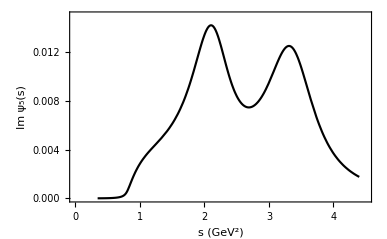
```mathematica
-Graphics-;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"StrangeHadronicSpectrumGraph.pdf"}],hadronicgraph];
```

## Graphing the quark mass range of stability

Graph depicting how the strange quark mass, m_s, (calculated using two different kernels) fluctuates over a range 2.5 GeV^2< s_0 < 5.0 GeV^2 . Note: s_0 is the radius of our circle in the complex energy plane.

### Contour Improved Perturbation Theory

```mathematica
ciptstabilitydata=Table[{i,CIPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,d2phi5]},{i,3,5.0,0.1}]
```

{{3., 99.8817}, {3.1, 99.218}, {3.2, 98.5482}, {3.3, 97.8653}, {3.4, 97.1649}, {3.5, 96.4478}, {3.6, 95.7211}, {3.7, 94.9959}, {3.8, 94.2838}, {3.9, 93.5957}, {4., 92.9402}, {4.1, 92.3243}, {4.2, 91.7532}, {4.3, 91.2313}, {4.4, 90.7619}, {4.5, 90.3478}, {4.6, 89.9916}, {4.7, 89.6957}, {4.8, 89.4624}, {4.9, 89.2941}, {5., 89.1935}}

```mathematica
ciptplot=ListLinePlot[{ciptstabilitydata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{2.95,5.05},{50,120}} ,PlotLabel->"Contour Improved Perturbation Theory"];
```

```mathematica
(*Calculating a typical error bar(at Subscript[s, 0] =4.2 GeV) to plot on ciptplot1*)
ms2error=MassErrorFESR[4.2,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi5];
```

```mathematica
(*Plotting error bars*)
cipterrorbars=ErrorListPlot[{{{4.2,ms2error[[1]][[1]]},ErrorBar[ms2error[[8]][[1]]]}},PlotStyle-> {Black,Directive[Thickness[0.002]]}];
ciptplot1=Show[ciptplot,cipterrorbars]
```

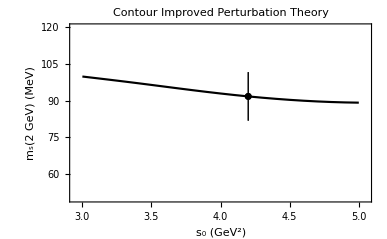
```mathematica
-Graphics-;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"StrangeCIPTGraph.pdf"}],ciptplot1];
```

### Fixed Order Perturbation Theory

```mathematica
foptstabilitydata=Table[{i,FOPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]},{i,3,5.0,0.1}]
```

{{3., 117.851}, {3.1, 118.269}, {3.2, 118.676}, {3.3, 119.069}, {3.4, 119.449}, {3.5, 119.822}, {3.6, 120.204}, {3.7, 120.616}, {3.8, 121.081}, {3.9, 121.622}, {4., 122.261}, {4.1, 123.019}, {4.2, 123.92}, {4.3, 124.986}, {4.4, 126.242}, {4.5, 127.718}, {4.6, 129.447}, {4.7, 131.469}, {4.8, 133.835}, {4.9, 136.608}, {5., 139.866}}

```mathematica
foptplot=ListLinePlot[{foptstabilitydata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{2.95,5.05},{80,150}}, PlotLabel->"Fixed Order Perturbation Theory"];
```

```mathematica
(*Calculating a typical error bar(at Subscript[s, 0] =4.2 GeV)to plot on foptplot1*)
ms2errorFOPT=MassErrorFESR[4.2,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi5A];
```

```mathematica
(*Plotting error bars*)
fopterrorbars=ErrorListPlot[{{{4.2,ms2errorFOPT[[1]][[1]]},ErrorBar[ms2errorFOPT[[8]][[1]]]}},PlotStyle-> {Black,Directive[Thickness[0.002]]}];
foptplot1=Show[foptplot,fopterrorbars]
```

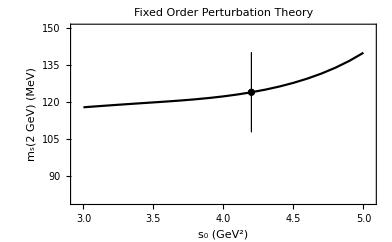
```mathematica
-Graphics-;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"StrangeFOPTGraph.pdf"}],foptplot1];
```

The  stability region of the Fixed Order Results is narrower than the stability of the Contour Improved Results.  Further, FOPT results in a larger uncertainty in the quark masses than CIPT, mainly caused by the importance FOPT places on the unknown higher order terms in the δPQCD series.

## Calculating the up and down quark mass with uncertainties

Calculating m_s(s) with uncertainties, at a scale s= (2 (GeV))^2. Set s_0 to be any value in the region of stability (between 2.5 GeV^2 and 5 GeV^2 for CIPT, with kernel P_5(s) = (s-a)(s-s_0)). For this calculation I choose, s_0 = 4.2 GeV^2.

```mathematica
Clear[s0];
s0=4.2;
```

### Contour Improved Perturbation Theory

```mathematica
msCIPT=CIPTmassFESR[s0,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,d2phi5]
msErrorCIPT =MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi5]
```

91.7532
{{91.7532, "Mass MeV"}, {-3.90084, "Δα"}, {-0.748765, "ΔGG"}, {2.65008, "Δs0"}, {89.6957, 94.9959, "Min s0 and Max s0"}, {8.15917, "Model Error"}, {-3.06425, "Unknown 6-loop PQCD term"}, {9.9379, "Total"}}

### Fixed Order Perturbation Theory

```mathematica
msFOPT=FOPTmassFESR[s0,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]
msErrorFOPT =MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi5A]
```

123.92
{{123.92, "Mass MeV"}, {-5.40776, "Δα"}, {-1.93973, "ΔGG"}, {5.42671, "Δs0"}, {120.616, 131.469, "Min s0 and Max s0"}, {11.0196, "Model Error"}, {-8.73797, "Unknown 6-loop PQCD term"}, {16.1319, "Total"}}

# Convergence

The δPQCD series is only known up to the α_s^4 term and does not appear to converge. In this section we examine  how this affects the quark masses calculated using Fixed Order Perturbation Theory and Contour Improved Perturbation Theory.

## Contour Improved Perturbation Theory: Graphing Convergence

```mathematica
Clear[s0];
s0=4.2;
```

```mathematica
(*The second derivative of the perturbative part of pseudoscalar correlator (d2phi5) is given below. It is written out explicitly to order:α^0/π,α/π, α^2/π, α^3/π respectively. (Note: the correlator to order α^4/π appears earlier in the notebook.) *)
d2phi51o[A_]:= {- 3/8*ms0^2/Pi^2*1/s*A};
d2phi52o[A_]:= - 3/8*ms0^2/Pi^2*1/s*(1+A*a*(11/3-2*Log[-s/muo^2] ));
d2phi53o[A_]:= - 3/8*ms0^2/Pi^2*1/s*(1+a*(11/3-2*Log[-s/muo^2] )
	+A*a^2*(5071/144-35/2*Zeta[3]-139/6*Log[-s/muo^2]+17/4*Log[-s/muo^2]^2));
d2phi54o[A_]:= - 3/8*ms0^2/Pi^2*1/s*(1+a*(11/3-2*Log[-s/muo^2] )
	+a^2*(5071/144-35/2*Zeta[3]-139/6*Log[-s/muo^2]+17/4*Log[-s/muo^2]^2)
	+A*a^3*(1995097/5184-1/36*π^4-65869/216*Zeta[3]+715/12*Zeta[5]-2720/9*Log[-s/muo^2]+475/4*Zeta[3]*Log[-s/muo^2]+695/8*Log[-s/muo^2]^2-221/24*Log[-s/muo^2]^3));
```

```mathematica
(*Calculating the quark mass Subscript[m, s], to each order of the perturbative correlator*)
(*Considering δPQCD up to term α^0/π*)
msconverge0=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi51o]
(*Considering δPQCD up to term α/π*)
msconverge1=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi52o]
(*Considering δPQCD up to term α^2/π*)
msconverge2=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi53o]
(*Considering δPQCD up to term α^3/π*)
msconverge3=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi54o]
(*Considering δPQCD up to term α^4/π*)
msconverge4=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,CIPTmassFESR,d2phi5]
```

```mathematica
(*Graphing the strange quark mass to each order*)
convCIPTplot=ErrorListPlot[{{{1,msconverge0[[1]][[1]]},ErrorBar[msconverge0[[8]][[1]]]},{{2,msconverge1[[1]][[1]]},ErrorBar[msconverge1[[8]][[1]]]},{{3,msconverge2[[1]][[1]]},ErrorBar[msconverge2[[8]][[1]]]},{{4,msconverge3[[1]][[1]]},ErrorBar[msconverge3[[8]][[1]]]},{{5,msconverge4[[1]][[1]]},ErrorBar[msconverge4[[8]][[1]]]}},AxesOrigin->{0,0}, Frame-> True,FrameLabel-> {None,"m_ud(2 GeV) (MeV)"},FrameStyle->Thick,FrameTicks->{{Automatic,None},{{{1,"O(α^0)"},{2,"O(α^1)"},{3,"O(α^2)"},{4,"O(α^3)"},{5," O(α^4)"}},None}},PlotStyle-> {Directive[Thickness[0.002],Black]},PlotRange-> {{0.8,5.2},{70,300}},PlotLegends->Placed[PointLegend[{"CIPT"}],{0.82,0.85}]]

Export[FileNameJoin[{NotebookDirectory[],"StrangeCIPTConvergeGraph.pdf"}],convCIPTplot];
```

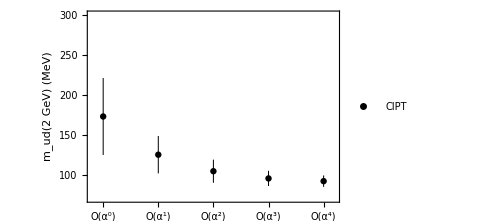
```mathematica
-Graphics-;
```

## Fixed Order Perturbation Theory: Graphing Convergence

```mathematica
(*The pseudoscalar correlator (phi5) is given below. It is written out explicitly to order:α^0/π,α/π, α^2/π, α^3/π respectively. (Note: the correlator to order α^4/π appears earlier in the notebook.)*)
phi51o[A_]= -ms0^2*s/(16*Pi^2)*A*(6*Log[-s/muo^2] -12 ); 
phi51Ao[A_]= phi51o[A]/ms0^2;

phi52o[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12+A*a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)); 
phi52Ao[A_]= phi52o[A]/ms0^2;

phi53o[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 +a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)+A*a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)); 
phi53Ao[A_]= phi53o[A]/ms0^2;
phi54o[A_]= -ms0^2*s/(16*Pi^2)*(6*Log[-s/muo^2] -12 +a*(-6*Log[-s/muo^2]^2+34*Log[-s/muo^2] -36.651)+a^2*(8.5*Log[-s/muo^2]^3-95*Log[-s/muo^2]^2+275.08*Log[-s/muo^2]-304.79)+A*a^3*(-13.813*Log[-s/muo^2]^4+229*Log[-s/muo^2]^3 -1165.4*Log[-s/muo^2]^2+2795.1*Log[-s/muo^2]-2966.2));
phi54Ao[A_]= phi54o[A]/ms0^2;

(*Calculating the quark mass Subscript[m, s], to each order of the perturbative correlator*)
(*Considering δPQCD up to term α^0/π*)
msconvergeFOPT0=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi51Ao];
(*Considering δPQCD up to term α/π*)
msconvergeFOPT1=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi52Ao];
(*Considering δPQCD up to term α^2/π*)
msconvergeFOPT2=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi53Ao];
(*Considering δPQCD up to term α^3/π*)
msconvergeFOPT3=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi54Ao];
(*Considering δPQCD up to term α^4/π*)
msconvergeFOPT4=MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi5A];
```

```mathematica
(*Graphing the strange quark mass to each order*)
convFOPTplot=ErrorListPlot[{{{1,msconvergeFOPT0[[1]][[1]]},ErrorBar[msconvergeFOPT0[[8]][[1]]]},{{2,msconvergeFOPT1[[1]][[1]]},ErrorBar[msconvergeFOPT1[[8]][[1]]]},{{3,msconvergeFOPT2[[1]][[1]]},ErrorBar[msconvergeFOPT2[[8]][[1]]]},{{4,msconvergeFOPT3[[1]][[1]]},ErrorBar[msconvergeFOPT3[[8]][[1]]]},{{5,msconvergeFOPT4[[1]][[1]]},ErrorBar[msconvergeFOPT4[[8]][[1]]]}},AxesOrigin->{0,0}, Frame-> True,FrameLabel-> {None,"m_ud(2 GeV) (MeV)"},FrameStyle->Thick,FrameTicks->{{Automatic,None},{{{1,"O(α^0)"},{2,"O(α^1)"},{3,"O(α^2)"},{4,"O(α^3)"},{5," O(α^4)"}},None}},PlotStyle-> {Directive[Thickness[0.002],Gray]},PlotRange-> {{0.8,5.2},{70,300}},PlotLegends->Placed[SwatchLegend[{"FOPT"},LegendMarkers->{"▲",11}],{0.83,0.73}],PlotMarkers->{"▲",11},Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing

Export[FileNameJoin[{NotebookDirectory[],"StrangeFOPTConvergeGraph.pdf"}],convFOPTplot];
```

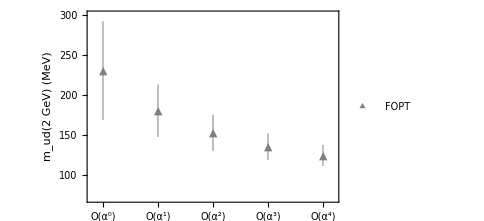
```mathematica
-Graphics-;
```

Comparing FOPT vs CIPT convergence

```mathematica
compareconvergence=Show[convCIPTplot,convFOPTplot]
Export[FileNameJoin[{NotebookDirectory[],"StrangeConvergeGraph.pdf"}],compareconvergence];
```

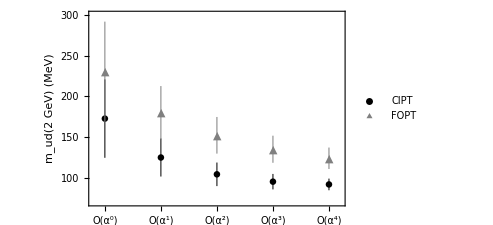
```mathematica
-Graphics-;
```

From the above graph one can see that the strange quark mass converges quicker when using the CIPT method: in the FOPT framework the quark mass changes  between the O(α^0) calculation and the O(α^4)calculation by 106 MeV; whereas in the CIPT framework the strange quark mass changes between the O(α^0) calculation and the O(α^4)calculation by 81 MeV.  
Therefore, CIPT places less importance on the unknown higher order terms in the δPQCD series, thereby reducing this uncertainty. The quark masses are calculated with a lower overall uncertainty in CIPT (as can be seen from the magnitude of the error bars in the above convergence graph).

# Comparisons

This section explores how the light quark mass changes if one uses: a different kernel or if one Taylor expands √δPQCD in order to examine the convergence of the series.

```mathematica
Clear[s0];
s0=4.2;
```

## Using different kernels

Various different kernels can be used in order to quench the hadronic resonances. Here we explore the effect of several different integration kernels on the stability of the quark mass. Since Contour Improved Perturbation Theory is our method of choice, we only use CIPT to examine the effects on m_s(s) this change will have.The first kernel (a), is the optimal kernel: P_5(s) = (s-a)(s-s_0) , which is explored in detail, earlier in this notebook. The second kernel (b), quenches the hadronic resonances at the two resonance peaks: P_5(s) = 1-a_0 s-a_1 s^2. This is the standard kernel which has been used before in determining the strange quark mass. Source: Dominguez, Nasrallah, Rontsch, Schilcher, ‘Strange quark mass from finite-energy QCD sum rules to five loops’ (2008). The third kernel (c), quenches the hadronic resonances at the two pionic resonance masses and at s_0: P_5(s) = (s-m_π1^2)(s-m_π2^2)(s_0-s). This is a pinched kernel which has been previously suggested to counteract potential duality violations . Source: Bodenstein, Dominguez, Schilcher, ‘Strange quark mass from sum rules with improved perturbative QCD convergence’ (2013).

```mathematica
(*Subscript[P, 5](s)= 1-Subscript[a, 0] s-Subscript[a, 1] s^2*)
a0C= 0.768;a1C = -0.140 ;
kern2[s_,s0_] := 1- a0C*s-a1C*s^2;
ciptdifkerneldata=Table[{i,CIPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern2,GluonCon,LQuarkCon,SQuarkCon,1,d2phi5]},{i,3,5.0,0.1}];
ciptplot2=ListLinePlot[{ciptdifkerneldata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{2.95,5.05},{70,140}}, PlotLabel->"CIPT with Kernel: P_5(s) = 1-a_0 s-a_1 s^2"];
```

```mathematica
(*Subscript[P, 5](s)= (s-Subscript[m, k1]^2)(s-Subscript[m, k2]^2)(Subscript[s, 0]-s)*)
kern3[s_,s0_]:= (s-mk1^2)*(s-mk2^2)*(s0-s);
ciptdifkerneldata3=Table[{i,CIPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern3,GluonCon,LQuarkCon,SQuarkCon,1,d2phi5]},{i,3,5.0,0.1}];
ciptplot3=ListLinePlot[{ciptdifkerneldata3},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{2.95,5.05},{70,140}}];
```

```mathematica
comparekernels=Show[ciptplot,ciptplot2,ciptplot3,Epilog->{Text["(a)",{3.25,102}],Text["(b)",{3.25,95}],Text["(c)",{3.25,85}]}]
Export[FileNameJoin[{NotebookDirectory[],"StrangeKernelGraph.pdf"}],comparekernels];
```

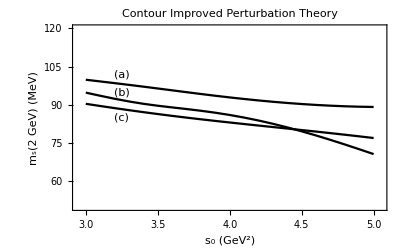
```mathematica
-Graphics-;
```

In the above graph: (a) P_5(s) = (s-a)(s-s_0), (b) P_5(s) = 1-a_0 s-a_1 s^2 and (c) P_5(s) = (s-m_k1^2)(s-m_k2^2)(s_0-s) .

From the above graph, we prefer kernel (a) P_5(s) = (s-a)(s-s_0) and (c) P_5(s) = (s-m_π1^2)(s-m_π2^2)(s_0-s) due to stability considerations. However, several other criteria are taken into account when deciding on the optimal kernel.  For instance, the kernel should not bring in higher dimensional condensates,  as their values are poorly known. This constrains substantially the powers of s. Hence, we are lead to disfavour kernel (c) since it results in the dimension d = 8 condensate entering the FESR (whose value is completely unknown), which would bring in an unknown systematic uncertainty into the calculation. Hence, our preferred kernel is kernel (a)P_5(s) = (s-a)(s-s_0), which quenches the hadronic resonance contribution at s=s_0,  as well as in the region between the two resonances.

## Taylor expanding √δPQCD series

Here, we Taylor expand the √δPQCD series in order to improve the convergence of this series.  The expressions for the series, before and after the Taylor expansion, can be found in the dissertation: Mes, ‘Light Quark Masses from QCD Finite Energy Sum Rules’, (2019). Here I examine numerical effect of performing the Taylor expansion on the strange quark mass m_s(s) and the region of stability. 
Note: This is done through using Fixed Order Perturbation Theory, since α_s is frozen around the circular contour; and this allows for series expansions in terms of α_s.

```mathematica
Clear[expand];
expand=-1/2;
```

```mathematica
(*Calculating Subscript[m, s](s)*)
```

```mathematica
msFOPTt=FOPTmassFESR[s0,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]
msErrorFOPTt =MassErrorFESR[s0,modelDPS[s,1,250,250,1],kern1,FOPTmassFESR,phi5A]
```

94.2212
{{94.2212, "Mass MeV"}, {-11.8471, "Δα"}, {-0.10392, "ΔGG"}, {4.24712, "Δs0"}, {87.6975, 96.1917, "Min s0 and Max s0"}, {8.37863, "Model Error"}, {-4.60626, "Unknown 6-loop PQCD term"}, {15.8057, "Total"}}

```mathematica
(*Note: the uncertainty due to the unknown higher order terms in the δPQCD series above, must be calculated manually*)
```

```mathematica
(*Graphically viewing the stability of the quark masses after taylor expanding the √δPQCD series*)
fopttaylordata=Table[{i,FOPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern1,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]},{i,2,5.0,0.1}]
```

```mathematica
foptplot2=ListLinePlot[{fopttaylordata},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.95,5.05},{50,120}}, PlotLabel->"Fixed Order Perturbation Theory with taylor expansion of√δPQCD series"];
```

```mathematica
(*Subscript[P, 5](s)= 1-Subscript[a, 0] s-Subscript[a, 1] s^2*)
a0C= 0.768;a1C = -0.140 ;
kern2[s_,s0_] := 1- a0C*s-a1C*s^2;
fopttaylordataB=Table[{i,FOPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern2,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]},{i,2,5.0,0.1}]
```

```mathematica
foptplot2B=ListLinePlot[{fopttaylordataB},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.95,5.05},{50,120}}, PlotLabel->"Fixed Order Perturbation Theory with taylor expansion of√δPQCD series"];
```

```mathematica
(*Subscript[P, 5](s)= (s-Subscript[m, k1]^2)(s-Subscript[m, k2]^2)(Subscript[s, 0]-s)*)
kern3[s_,s0_]:= (s-mk1^2)*(s-mk2^2)*(s0-s);
fopttaylordataC=Table[{i,FOPTmassFESR[i,aint0,sint0,modelDPS[s,1,250,250,1],kern3,GluonCon,LQuarkCon,SQuarkCon,1,phi5A]},{i,2,5.0,0.1}]
```

```mathematica
foptplot2C=ListLinePlot[{fopttaylordataC},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_s(2 GeV) (MeV)"},PlotStyle-> {Directive[Thickness[0.004],Black], Directive[Thickness[0.004],Black]},PlotRange-> {{1.95,5.05},{50,120}}, PlotLabel->"Fixed Order Perturbation Theory with taylor expansion of√δPQCD series"];
```

```mathematica
comparekernelstaylor=Show[foptplot2,foptplot2B,foptplot2C,Epilog->{Text["(a)",{3.25,100}],Text["(c)",{3.25,93}],Text["(b)",{3.25,80}]}]
Export[FileNameJoin[{NotebookDirectory[],"StrangeTaylorKernelGraph.pdf"}],comparekernelstaylor];
```

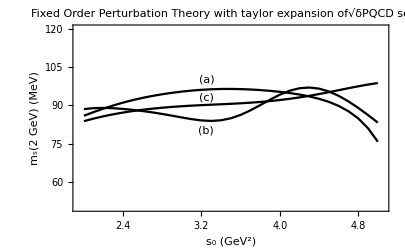
```mathematica
-Graphics-;
```

In the above graph: (a) P_5(s) = (s-a)(s-s_0), (b) P_5(s) = 1-a_0 s-a_1 s^2 and (c) P_5(s) = (s-m_k1^2)(s-m_k2^2)(s_0-s) .

The strange quark mass m_s(s), that is calculated by applying the Taylor expansion to the√δPQCD series is much smaller than our previous determinations using FOPT. The behaviour of m_s(s) over a range of s values has also changed, and the stability region has narrowed considerably (between 3 < s_0< 3.5 GeV). It is interesting to note that using the Taylor expansion to improve the convergence (within the FOPT framework) results in a value of the  strange quark mass m_s(s) , which is comparable to m_s(s) determined in the CIPT framework. In both cases, the value of the strange quark mass m_s(s), is in close agreement with Lattice QCD. While the strange quark determined within the FOPT framework (without the Taylor expansion applied) is some 20 MeV larger.
The method preferred by the author for the final determination of m_s(s) is CIPT, due to the wider stability window, smaller variation under the uncertainty in the strong coupling α_s, and the competitive convergence which is studied at each order of the √δPQCD series.